# Scalar perturbations in inflation and reheating

This notebook was used for producing results in PhD thesis [1], based on papers [2] and [3]:

[1]  A. Rogelj, Scalar perturbations in warm inflation and during reheating, PhD thesis, University of Bern, Switzerland (2026) [https://doi.org/10.48620/101166 ].
[2] M. Laine, S. Procacci and A. Rogelj, Evolution of coupled scalar perturbations through smooth reheating. II. Thermal fluctuation regime, JCAP 12, ID (2025) [https://iopscience.iop.org/article/10.1088/1475-7516/2025/12/058 ].
[3] M. Laine, S. Procacci and A. Rogelj, Evolution of coupled scalar perturbations through smooth reheating. I. Dissipative regime, JCAP 10, ID (2024) [https://iopscience.iop.org/article/10.1088/1475-7516/2024/10/040 ].

## Model-dependent inputs

### model parameters

fixed coefficients

```mathematica
gstar=106.75 (*d.o.f.*);
Nc=3;(*number of colors - enters Υ*)
Nf=5; (*numer of flavours - enters Υ*)
mpl=1;(*units of Plack mass everywhere*)
```

functions

```mathematica
er[Te_]:=(gstar π^2 Te^4)/30(*radiation energy density*)
pr[Te_]:=(gstar π^2 Te^4)/90(*radiation pressure*)
V[ϕ_,Te_]:=λ ϕ^4
Υ[ϕ_,Te_,depvar_]:=Te^2/(2fa^2)(1/(α^5  Nc^5 Te) +(2Nf)/(Nc H[ϕ,Te,depvar]) )^(-1)(*friction*)
(*depvar is just time. We define H in this way such that in early times background equations we can easily take time derivatives of functions H depends on*)
```

### initial values

```mathematica
(*k/aH ratio at which you wish to start/finish computing power spectrum*)
whentostart = 10^2;
whentofinish = 10^-10;
```

```mathematica
ϕref=7 mpl;(*ϕ at reference time, when we start background evolution; choose such that there are enough e-folds of inflation*)
```

```mathematica
kamode=4.1 10^(-39) mpl;(*physical momentum when T=10^(-12) Planck mass*)
```

### numerical parameters

If using the code for the first time: just keep the suggested values.

```mathematica
tilt=0.1; (*parameter for computing spectral tilt; denoted by δ_t in eq. (7.13) in ref [1]*)
nPoints=200;(*how many points to plot in power spectrum graph*)
n=3; (*tolerance, see eq. (7.9) of ref [1]. Lower value=possibly worse accuracy, higher value=longer computation time.*)
δ=10^-15;(*handling singularities; see Ch. 8.1 of [1]. Vary to make sure the results do not depend on it.*)
kastarttime=10;(*value of t/tref after which we start searching for the initial time of integration of curvature perturbations; bigger value better numerically; no result if too big*)
kastep=50;(*searches for horizon crossing value & whentostart and whentofinish times in the intervals of this many trefs*)
interp=30; (*Directly evaluating time step sizes according to eq. (7.9) from ref. [1] is numerically expensive. Instead find the sizes of time steps in intervals of 'interp'-30 seems to give accurate results without becoming excessively slow. Then interpolate the result.*)
```

### parameter scan

Write a control notebook iterating through your desired set of model parameters, or just choose to a single set of parameters at a time, e.g. by writing j=1 / by supplying one specific set of model parameters.

```mathematica
λlist:={10^(-21),10^(-20),10^(-19),10^(-18),10^(-17),10^(-16),10^(-15),10^(-21),10^(-20),10^(-19),10^(-18),10^(-17),10^(-16),10^(-15)}
falist:={0.146,0.264,0.518,1.05,2.3,4.95,8.69,0.153,0.278,0.516,1.025,2.27,4.98,8.56}
αslist:={0.0269,0.0263,0.0257,0.0251,0.0246,0.0243,0.0242,0.0269,0.0263,0.0257,0.0251,0.0246,0.0243,0.0242}
```

```mathematica
j=8;(*which entity is chosen from the list*)
λ=λlist[[j]];
fa=falist[[j]]8.19 10^(-8);
α=αslist[[j]];
```

### save results

```mathematica
(*where to export results*)
directoryPath="/local_scratch/rogelj/"; 

(*give a name to background and power spectrum plots; here named according to model parameters λ and fa*)
fileNameBckPlot=StringJoin["SM_λ_10^-",ToString[-Log[10,λ]],"_fa_",ToString[falist[[j]]],"_background_plot.pdf"];
fileNamePowerSpectrumPlot=StringJoin["SM_λ_10^-",ToString[-Log[10,λ]],"_fa_",ToString[falist[[j]]],"_perturbations_plot.pdf"];
```

```mathematica
(*give names to datafiles, save them as .wxf files*)
fileNameTable=StringJoin["SM_λ_10^-",ToString[-Log[10,λ]],"_fa_",ToString[falist[[j]]],"_.wxf"];(*key freeze-out quantities*)
fileNameBck=StringJoin["SM_λ_10^-",ToString[-Log[10,λ]],"_fa_",ToString[falist[[j]]],"_full_background.wxf"]; (*full background data*)
fileNamePowerSpectrum=StringJoin["SM_λ_10^-",ToString[-Log[10,λ]],"_fa_",ToString[falist[[j]]],"_full_perturbations.wxf"];(*full perturbations data*)
```

```mathematica
(*suppress benign notifications*)
Off[NDSolve::precw];
Off[FindRoot::precw];
```

## Computing: background and perturbations

### background: early times

```mathematica
(*standard thermodynamics*)
eav[ϕ_,Te_]:=er[Te]+V[ϕ,Te]-Te Derivative[0,1][V][ϕ,Te](*average energy density*)
pav[ϕ_,Te_]:=pr[Te]-V[ϕ,Te](*average pressure*)
```

derive initial values at reference time

```mathematica
Clear[Tref];
tref=SetPrecision[Sqrt[3/(8π V[ϕref,Tref])]mpl,50];
Href=1/tref;(*H at ref time*)
Υref[Tref_]:=Υ[ϕ,Te,depvar]/.{Te->Tref,ϕ->ϕref,H[ϕ,Te,depvar]->Href};
ϕdotref[Tref_]:=- Derivative[1,0][V][ϕref,Tref]tref/(3Href +Υref[Tref]);
```

find initial temperature

```mathematica
Quiet[SafeTrefSolve[]:=Module[
(*internally define variables*)
{T0,sols,filteredSols,relImag,bestSol},
(*solve for initial temperature; eq. (9.8) from [1]]*)T0=Quiet@NSolve[3 Href (pr[Tref]+er[Tref])==ϕdotref[Tref]^2 Υref[Tref]/tref^2,Tref];
(*write solutions as a list*)
sols=Replace[Tref/. T0,x_/;AtomQ[x]:>{x}];(*solution is T; we expect this to be a numerical value with real part between 0 and 1 Planck mass*)filteredSols=Select[sols,NumericQ[#]&&0<Re[#]<1&];
(*check if multiple solutions fit this criteria*)
If[Length[filteredSols]>0,
(*if yes: pick the most sensible solution = fully real/least imaginary one*)relImag=Abs[Im[#]]/Abs[Re[#]]&/@filteredSols;
bestSol=filteredSols[[First@Ordering[relImag,1]]];
(*take its real part as your initial temperature guess*)
Re[bestSol],
(*if no: default to 10^-5, which is usually an acceptable starting point*)
Print["[Warning] Tref defaulted to 10^-5"];
10^-5]],{Select::normal}]

Tref=SafeTrefSolve[];
```

define background equations

```mathematica
H[ϕ_,Te_,depvar_]:=1/mpl 2 √((2 π)/3) √(er[Te]+V[ϕ,Te]+1/2 D[ϕ,depvar]^2/tref^2-Te Derivative[0,1][V][ϕ,Te])
```

```mathematica
BackgroundEquation1[t_]:=ϕ''[t]==-(3H[ϕ[t],Te[t],t]+Υ[ϕ[t],Te[t],t])ϕ'[t]tref-tref^2 Derivative[1,0][V][ϕ[t],Te[t]] ;
BackgroundEquation2[t_]:=D[er[Te[t]],t]==-3H[ϕ[t],Te[t],t]tref(er[Te[t]]+pr[Te[t]]-Te[t]D[ V[ϕ[t],Te[t]],Te[t]])+Te[t]D[ V[ϕ[t],Te[t]],Te[t],t]+Υ[ϕ[t],Te[t],t]ϕ'[t]^2/tref ;
initialconditionsTϕ={ϕ[1]==ϕref,Te[1]==Tref,ϕ'[1]==ϕdotref[Tref]};
```

solve background equations

```mathematica
Quiet[Module[{count=0},bckfull=NDSolve[{BackgroundEquation1[t],BackgroundEquation2[t],initialconditionsTϕ,WhenEvent[(1/2 ϕ'[t]^2/tref^2+V[ϕ[t],Te[t]]-Te[t]Derivative[0,1][V][ϕ[t],Te[t]])/er[Te[t]]<=10^(-1),"StopIntegration"]},{ϕ,Te},{t,1,10^20},AccuracyGoal->25,PrecisionGoal->10,MaxSteps->10^9,WorkingPrecision->50]]];
```

store key background quantities

```mathematica
ϕbcksol=bckfull[[1,1,2]];
ϕbck1[t_]:=ϕbcksol[t]
```

```mathematica
Tbcksol=bckfull[[1,2,2]];
Tbck1[t_]:=Tbcksol[t];
```

```mathematica
ts=ϕbck1["Domain"][[1,2]];(*time at which we stop early time integration*)
```

### background: late times

background averaged equations

```mathematica
Hlate[Te_]:=Sqrt[8π/3]Sqrt[er[Te]]/mpl
```

```mathematica
(*will be optimized for potentials inducing early matter domination*)
Module[{count=0},bckfull2=NDSolve[{D[er[Te[t]],t]/tref+3Hlate[Te[t]](er[Te[t]]+pr[Te[t]])==0,Te[ts]==Tbck1[ts],
WhenEvent[Te[t]==10^-12,"StopIntegration"]},{ϕ,Te,ka},{t,ts,10^30},AccuracyGoal->50,PrecisionGoal->10,MaxSteps->10^9,WorkingPrecision->50]];
```

store key background quantities

```mathematica
Tbcksol2=bckfull2[[1,2,2]];
Tbck2[t_]:=Tbcksol2[t]
```

```mathematica
te=Tbck2["Domain"][[1,2]];(*time at which we stop late time integration*)
```

construct continuous functions from key background quantities

```mathematica
Tbck[t_]:=If[t<=ts,Tbck1[t],Tbck2[t]];
ϕbck[t_]:=If[t<=ts,ϕbck1[t],0];
```

obtain all relevant background quantities

```mathematica
Hbck[t_]:=(H[ϕbck[tt],Tbck[tt],tt]/.tt->t);
```

```mathematica
Υ[ϕbck[t],Tbck[t],t];
Υbck[t_]:=Evaluate[%]
```

```mathematica
F[t_]:=(-Hbck'[t]/Hbck[t]+ϕbck''[t]/(ϕbck'[t]+I δ tref))/tref
```

```mathematica
D[ϕbck[t],t];
ϕdot[t_]:=Evaluate[%]
```

```mathematica
D[ϕbck[t],t,t];
ϕdotdot[t_]:=Evaluate[%]
```

```mathematica
D[ϕbck[t],t,t,t];
ϕdotdotdot[t_]:=Evaluate[%]
```

```mathematica
D[Tbck[t],t];
Tdot[t_]:=Evaluate[%]
```

```mathematica
D[Hbck[t],t];
Hdot[t_]:=Evaluate[%]
```

```mathematica
D[Υ[ϕbck[t],Tbck[t],t],Tbck[t]];
ΥTder[t_]:=Evaluate[%]
```

```mathematica
pav[t_]:=pav[ϕbck[t],Tbck[t]]
eav[t_]:=eav[ϕbck[t],Tbck[t]]
```

### momentum evolution

```mathematica
Quiet[NDSolve[{D[kal[t],t]==-Hbck[t]tref,kal[te]==Log[kamode]},kal,{t,1,te},PrecisionGoal->10,AccuracyGoal->10,WorkingPrecision->50][[1,1,2]]][t];
kabck1[t_]:=Evaluate[%]
```

```mathematica
kabck[t_]:=Evaluate[Exp[kabck1[t]]](*physical momentum, k/a*)
```

Find time at which to start (ti) and end (tf) the perturbative evolution, as well as the time of the horizon crossing (tmatch).
The  cells below first tries to find approximate times, and then finds the exact values. That is because FindRoot is very slow if we do not provide a narrow interval in which the root is suppose to lie.

```mathematica
(*finds an interval in which a 'function' (such as k/(a H))  obtains its 'target' value, provided this value is achieved after time 'tinit'; searching for that interval is done in the increments of 'step'*)
findBracket[func_,target_,tinit_,step_]:=Module[
{t1=tinit,t2=tinit,v1,v2},
(*v1 will be the value of function at the time we start the computation*)
v1=func[t1];
(*v2 will be the value of function at a later time*)
v2=v1;
While[
Sign[v1-target]==Sign[v2-target],
t2+=step;
v2=func[t2];
(*stop computation when function crosses the target value*)
 (*in case something goes wrong, the code should not run indefinitely*)
If[Abs[t2]>te,Break[]];
];
(*save the interval of size 'step' in which function obtains the target value*)
{t2-step,t2}]

ratio[t_]:=Evaluate[kabck[t]/Hbck[t]]

(*find the exact values with FindRoot, based on the interval from findBracket*)
(*start power spectrum evolution*)
ti=FindRoot[ratio[t]==whentostart,{t,Sequence@@findBracket[ratio,whentostart,kastarttime,2 kastep]}][[1,2]];
(*horizon exit*)
tmatch=FindRoot[ratio[t]==1,{t,Sequence@@findBracket[ratio,1,ti,kastep]}][[1,2]];
(*end power spectrum evolution*)
tf=FindRoot[ratio[t]==whentofinish,{t,Sequence@@findBracket[ratio,whentofinish,tmatch,kastep]}][[1,2]];
```

### determine time steps

define matrix, eq. (7.3) from [1]

```mathematica
G=1/mpl^2;
```

```mathematica
-kabck[t]^2 tref^2;
c1[t_]:=Evaluate[%]
```

```mathematica
-tref (Υbck[t]+3Hbck[t]+2F[t]);
c2[t_]:=Evaluate[%]
```

```mathematica
4π G tref^2(Υbck[t]+2F[t])/Hbck[t];
c3[t_]:=Evaluate[%]
```

```mathematica
-tref^2(4π G(1-D[pav[ϕbck,Tbck[t]],Tbck[t]]/D[eav[ϕbck,Tbck[t]],Tbck[t]])/Hbck[t]+(ΥTder[t]ϕdot[t]/tref+Derivative[1,1][V][ϕbck[t],Tbck[t]])/(ϕdot[t]D[eav[ϕbck,Tbck[t]],Tbck[t]]/tref));
c4[t_]:=Evaluate[%]
```

```mathematica
-(eav[t]+pav[t]);
d2[t_]:=Evaluate[%]
```

```mathematica
-tref(3Hbck[t]+4π G ϕdot[t]^2/(Hbck[t]tref^2));
d3[t_]:=Evaluate[%]
```

```mathematica
tref(D[pav[ϕbck,Tbck[t]],Tbck[t]]/D[eav[ϕbck,Tbck[t]],Tbck[t]]);
d4[t_]:=Evaluate[%]
```

```mathematica
-tref kabck[t]^2(eav[t]+pav[t]);
e1[t_]:=Evaluate[%]
```

```mathematica
(Υbck[t]ϕdot[t]^2/tref^2+8π G eav[t](eav[t]+pav[t])/Hbck[t]);
e2[t_]:=Evaluate[%]
```

```mathematica
-tref ( kabck[t]^2+4π G (Υbck[t]ϕdot[t]^2/tref^2+8π G eav[t](eav[t]+pav[t])/Hbck[t])/Hbck[t]);
e3[t_]:=Evaluate[%]
```

```mathematica
tref((Hdot[t]/tref-4π G(eav[t]+pav[t]))/Hbck[t]-3Hbck[t](1+D[pav[ϕbck,Tbck[t]],Tbck[t]]/D[eav[ϕbck,Tbck[t]],Tbck[t]])+ΥTder[t]ϕdot[t]^2/(D[eav[ϕbck[t],Tbck[t]],Tbck[t]]tref^2)+Derivative[1,1][V][ϕbck[t],Tbck[t]]ϕdot[t]/(tref D[eav[ϕbck[t],Tbck[t]],Tbck[t]]));
e4[t_]:=Evaluate[%]
```

```mathematica
Matr[t_]:={{0,1,0,0},{c1[t],c2[t],c3[t],c4[t]},{0,d2[t],d3[t],d4[t]},{e1[t],e2[t],e3[t],e4[t]}};
```

define step sizes based on the matrix

```mathematica
ε[t_,n_]:=10^(-n)/Max[Abs/@Eigenvalues[Matr[t]]]
```

Directly evaluating ε is numerically expensive.
Find the sizes of time steps in intervals of ‘interp’ , then interpolate the result. Use Log as the step sizes are very small at first; it additionally ensures ε is interpolated to positive values.

```mathematica
Quiet[Interpolation[
Table[{i,Log[ε[i,n]]},{i,ti,tf+interp+5,interp}]
][t]];
εapprox1[t_]:=Evaluate[%]
εapprox[t_]:=Exp[εapprox1[t]]
```

```mathematica
TimeSteps[t0_,tf_]:=Module[{t=SetPrecision[t0,50],dt},
Reap[While[t<=tf+10^(-n),
dt=SetPrecision[εapprox[t],50];
Sow[{t,dt}];
t+=dt];][[2,1]]]//Transpose
```

```mathematica
{times,dts}=TimeSteps[ti,tf];
```

### tabulate background

#### tabulate basic quantities

dictionary:
s at the end = tabulated values
dot = time derivative 
derT = derivative w.r.t. temperature

derivatives are w.r.t. t/tref.

```mathematica
ϕs=ϕbck/@times;
```

```mathematica
ϕdot1=(ϕs[[3;;]]-ϕs[[;;-3]])/(dts[[;;-3]]+dts[[2;;-2]]);
ϕdots=Append[Prepend[ϕdot1,ϕdot1[[1]]],ϕdot1[[-1]]];
```

```mathematica
ϕdott1=(ϕdots[[3;;]]-ϕdots[[;;-3]])/(dts[[;;-3]]+dts[[2;;-2]]);
ϕdotdots=Append[Prepend[ϕdott1,ϕdott1[[1]]],ϕdott1[[-1]]];
```

```mathematica
ϕdottt1=(ϕdotdots[[3;;]]-ϕdotdots[[;;-3]])/(dts[[;;-3]]+dts[[2;;-2]]);
ϕdotdotdots=Append[Prepend[ϕdottt1,ϕdottt1[[1]]],ϕdottt1[[-1]]];
```

```mathematica
Ts=Tbck/@times;
```

```mathematica
Hs=1/mpl 2 √((2 π)/3) √(er[Ts]+V[ϕs,Ts]+1/2 ϕdots^2/tref^2-T Derivative[0,1][V][ϕs,Ts]);
```

```mathematica
Hdots=-4π G ((ϕdots/tref)^2+eav[ϕs,Ts]+pav[ϕs,Ts])tref;(*derivative is w.r.t. t/tref*)
```

```mathematica
Υs=Υ[ϕ,Te,tt]/.{Te->Ts,ϕ->ϕs};
```

```mathematica
ΥdotT=D[Υ[ϕ,Tem,tt],Tem]//Simplify;
υdots=ΥdotT/.{Tem->Ts,ϕ->ϕs};
ΥderTs=υdots;(*T derivative of friction Υ*)
```

```mathematica
deriveeav=D[eav[ϕ,Tempr],Tempr]//Simplify;
tempderiveeav=deriveeav/.{Tempr->Ts,ϕ->ϕs};
ederTs=tempderiveeav; (*T derivative of background energy density*)
```

```mathematica
derivepav=D[pav[ϕ,Tee],Tee]//Simplify;
tempderivepav=derivepav/.{Tee->Ts,ϕ->ϕs};
pderTs=tempderivepav; (*T derivative of background pressure*)
```

```mathematica
Tdot1=(Ts[[3;;]]-Ts[[;;-3]])/(dts[[;;-3]]+dts[[2;;-2]]);
Tdots=Append[Prepend[Tdot1,Tdot1[[1]]],Tdot1[[-1]]];
```

```mathematica
erdots=D[er[Temp[timee]],timee]/tref/.{Temp'[timee]->Tdots,Temp[timee]->Ts};
```

```mathematica
Hdott1=(Hdots[[3;;]]-Hdots[[;;-3]])/(dts[[;;-3]]+dts[[2;;-2]]);
Hdotdots=Append[Prepend[Hdott1,Hdott1[[1]]],Hdott1[[-1]]];
```

```mathematica
Fs=1/tref (-Hdots/Hs+ϕdotdots/(ϕdots+I δ tref));
```

```mathematica
Fdots=1/tref (-Hdotdots/Hs+(Hdots/Hs)^2+ϕdotdotdots/(ϕdots+ I δ tref)-ϕdotdots^2/(ϕdots^2+2I δ tref ϕdots));(*derivative is w.r.t. t/tref*)
```

```mathematica
VderTϕs=Derivative[1,1][V][ϕs,Ts];
```

#### tabulate momentum, noise autocorrelator, form matrix elements

In order to compute the spectral tilt, power spectra need to be computed also for a slightly larger and slightly smaller k/a. We evaluate all quantities which are sensitive to k/a three times (the additional two evaluations are always in blue boxes; higher momentum evaluations end with p, lower with m).

k/a and the noise

```mathematica
kas=kabck/@times;(*k/a list*)
```

```mathematica
kasp=10^(tilt) kabck/@times(*slightly larger k/a*);
kasm=10^(-tilt) kabck/@times(*slightly smaller k/a*);
```

```mathematica
ϵks=Re[Sqrt[kas^2-(Υs+Fs+2Hs)(Fs+Hs)-(Hdots/tref+Fdots/tref)]];
```

```mathematica
ϵksp=Re[Sqrt[kasp^2-(Υs+Fs+2Hs)(Fs+Hs)-(Hdots/tref+Fdots/tref)]];
ϵksm=Re[Sqrt[kasm^2-(Υs+Fs+2Hs)(Fs+Hs)-(Hdots/tref+Fdots/tref)]];
```

```mathematica
Ωks=Quiet[N[2 Υs kas^3 ϵks/(2 π^2 (Exp[ϵks/Ts]-1)),50],General::munfl];
```

```mathematica
Ωksp=Quiet[N[2 Υs kasp^3 ϵksp/(2 π^2 (Exp[ϵksp/Ts]-1)),50],General::munfl];
Ωksm=Quiet[N[2 Υs kasm^3 ϵksm/(2 π^2 (Exp[ϵksm/Ts]-1)),50],General::munfl];
```

matrix elements, no k/a

```mathematica
c2s=-tref (Υs+3Hs+2Fs);
c3s=4π G tref^2(Υs+2Fs )/Hs;
c4s=-tref^2(4π G(1-pderTs/ederTs)/Hs+(ΥderTs ϕdots/tref+VderTϕs)/(ederTs ϕdots/tref));
d2s=-(eav[ϕs,Ts]+pav[ϕs,Ts]);
d3s=-tref(3Hs+4π G ϕdots^2/(Hs tref^2));
d4s=tref pderTs/ederTs;
e2s=Υs ϕdots^2/tref^2+8π G eav[ϕs,Ts](eav[ϕs,Ts]+pav[ϕs,Ts])/Hs;
e4s=tref((Hdots/tref-4π G(eav[ϕs,Ts]+pav[ϕs,Ts]))/Hs -3Hs (1+pderTs/ederTs)+ΥderTs ϕdots^2/(ederTs tref^2)+VderTϕs ϕdots/(tref ederTs));
```

matrix elements, with k/a

```mathematica
c1s=-kas^2 tref^2;
```

```mathematica
c1sp=10^(2tilt)c1s;
c1sm=10^(-2tilt)c1s;
```

```mathematica
e1s=-tref kas^2(eav[ϕs,Ts]+pav[ϕs,Ts]);
```

```mathematica
e1sp=10^(2tilt)e1s;
e1sm=10^(-2tilt)e1s;
```

```mathematica
e3s=-tref(kas^2+4π G(Υs ϕdots^2/tref^2+8π G eav[ϕs,Ts](eav[ϕs,Ts]+pav[ϕs,Ts])/Hs )/Hs );
```

```mathematica
e3sp=-tref(kasp^2+4π G(Υs ϕdots^2/tref^2+8π G eav[ϕs,Ts](eav[ϕs,Ts]+pav[ϕs,Ts])/Hs )/Hs );
e3sm=-tref(kasm^2+4π G(Υs ϕdots^2/tref^2+8π G eav[ϕs,Ts](eav[ϕs,Ts]+pav[ϕs,Ts])/Hs )/Hs );
```

### compute power spectrum average

#### initial values

```mathematica
Rinit[start_]:=-(tref Hbck[start])/((ϕbck'[start]+I 0 tref) 2π)kabck[start]
Rpinit[start_]:=(tref^2 Hbck[start] I)/((ϕbck'[start]+I 0 tref) 2π)kabck[start]^2
Svinit[start_]:=0
STinit[start_]:=0
```

#### matrix formalism

```mathematica
M[i_]:=M[i]={{0,1,0,0},{c1s[[i]],c2s[[i]],c3s[[i]],c4s[[i]]},{0,d2s[[i]],d3s[[i]],d4s[[i]]},{e1s[[i]],e2s[[i]],e3s[[i]],e4s[[i]]}}
MT[i_]:=Conjugate[Transpose[M[i]]]
Ncoeff[i_]:=Ncoeff[i]= {{0,0,0,0},{0,tref^4 Abs[Hs[[i]]tref/(ϕdots[[i]]+I δ tref)]^2,0,-Hs[[i]]^2 tref^3},{0,0,0,0},{0,-Hs[[i]]^2 tref^3,0,Hs[[i]]^2ϕdots[[i]]^2}}
Noise[i_]:=Noise[i]=Ωks[[i]]/tref
SolMatrix=ConstantArray[0,{Length[times],4,4}](*solution matrix*);
SolMatrix[[1]]={{Rinit[ti]},{Rpinit[ti]},{Svinit[ti]},{STinit[ti]}}.{{Conjugate[Rinit[ti]],Conjugate[Rpinit[ti]],Conjugate[Svinit[ti]],Conjugate[STinit[ti]]}}(*inital conditions*);
```

```mathematica
(*find solutions*)
Quiet[
N[
With[{Id=IdentityMatrix[4]},Do[SolMatrix[[i+1]]=(Id+dts[[i]] M[i]).SolMatrix[[i]].(Id+dts[[i]] MT[i])+dts[[i]] Ncoeff[i] Noise[i],{i,Length[times]-1}]
],50],General::munfl]
```

Only plot solutions at specific times, ‘inds’.

```mathematica
(*create time points for graph plotting, logarithmically spaced*)
timesLog=Log[times];
logMinn=First[timesLog];
logMaxn=Last[timesLog];
edges=Subdivide[logMinn,logMaxn,nPoints];(*log-chosen time point to plot*)

(*'edges' need not coincide with 'times' - find 'times' points at/just after the suggested 'edges' time values = inds*)
inds=Reap[Module[{i=1},
Do[While[i<Length[timesLog]&&timesLog[[i]]<edge,i++];
If[i<=Length[timesLog],Sow[i]],{edge,edges}]]][[2,1]];
inds=DeleteDuplicates[inds];

(*compute background at inds needed to plot curvature instead of isocurvature pert.*)
denvArray=eav[ϕs,Ts]+pav[ϕs,Ts];  
denTArray=ederTs*Tdots/tref;            
denvSample=denvArray[[inds]];
denTSample=denTArray[[inds]];
```

define curvature power spectrum to plot

```mathematica
PRv=Re@(SolMatrix[[inds,1,1]]+(SolMatrix[[inds,1,3]]+SolMatrix[[inds,3,1]])/denvSample+SolMatrix[[inds,3,3]]/denvSample^2);

PRT=Re@(SolMatrix[[inds,1,1]]+(SolMatrix[[inds,1,4]]+SolMatrix[[inds,4,1]])/denTSample+SolMatrix[[inds,4,4]]/denTSample^2);
PRϕ=Re@SolMatrix[[inds,1,1]];
```

#### spectral tilt

Forward  step

```mathematica
Mp[i_]:=Mp[i]={{0,1,0,0},{c1sp[[i]],c2s[[i]],c3s[[i]],c4s[[i]]},{0,d2s[[i]],d3s[[i]],d4s[[i]]},{e1sp[[i]],e2s[[i]],e3sp[[i]],e4s[[i]]}}
MTp[i_]:=Conjugate[Transpose[Mp[i]]]
Noisep[i_]:=Noisep[i]=Ωksp[[i]]/tref
SolMatrixp=ConstantArray[0,{Length[times],4,4}];
SolMatrixp[[1]]={{Rinit[ti]},{Rpinit[ti]},{Svinit[ti]},{Svinit[ti]}}.{{Conjugate[Rinit[ti]],Conjugate[Rpinit[ti]],Conjugate[Svinit[ti]],Conjugate[Svinit[ti]]}};
```

```mathematica
(*find solutions*)
Quiet[N[With[{Id=IdentityMatrix[4]},Do[SolMatrixp[[i+1]]=(Id+dts[[i]] Mp[i]).SolMatrixp[[i]].(Id+dts[[i]] MTp[i])+dts[[i]] Ncoeff[i] Noisep[i],{i,Length[times]-1}]],50],
General::munfl]
```

```mathematica
(*define curvature power spectrum for spectral tilt/optional plotting*)
PRvp=Re@(SolMatrixp[[inds,1,1]]+(SolMatrixp[[inds,1,3]]+SolMatrixp[[inds,3,1]])/denvSample+SolMatrixp[[inds,3,3]]/denvSample^2);

PRTp=Re@(SolMatrixp[[inds,1,1]]+(SolMatrixp[[inds,1,4]]+SolMatrixp[[inds,4,1]])/denTSample+SolMatrixp[[inds,4,4]]/denTSample^2);
PRϕp=Re@SolMatrixp[[inds,1,1]];
```

Backwards  step

```mathematica
Mm[i_]:=Mm[i]={{0,1,0,0},{c1sm[[i]],c2s[[i]],c3s[[i]],c4s[[i]]},{0,d2s[[i]],d3s[[i]],d4s[[i]]},{e1sm[[i]],e2s[[i]],e3sm[[i]],e4s[[i]]}}
MTm[i_]:=Conjugate[Transpose[Mm[i]]]
Noisem[i_]:=Noisem[i]=Ωksm[[i]]/tref
SolMatrixm=ConstantArray[0,{Length[times],4,4}];
SolMatrixm[[1]]={{Rinit[ti]},{Rpinit[ti]},{Svinit[ti]},{Svinit[ti]}}.{{Conjugate[Rinit[ti]],Conjugate[Rpinit[ti]],Conjugate[Svinit[ti]],Conjugate[Svinit[ti]]}};
```

```mathematica
(*find solutions*)
Quiet[
N[
With[{Id=IdentityMatrix[4]},Do[SolMatrixm[[i+1]]=(Id+dts[[i]] Mm[i]).SolMatrixm[[i]].(Id+dts[[i]] MTm[i])+dts[[i]] Ncoeff[i] Noisem[i],{i,Length[times]-1}]],50],
General::munfl]
```

```mathematica
(*define curvature power spectrum for spectral tilt/optional plotting*)
PRvm=Re@(SolMatrixm[[inds,1,1]]+(SolMatrixm[[inds,1,3]]+SolMatrixm[[inds,3,1]])/denvSample+SolMatrixm[[inds,3,3]]/denvSample^2);

PRTm=Re@(SolMatrixm[[inds,1,1]]+(SolMatrixm[[inds,1,4]]+SolMatrixm[[inds,4,1]])/denTSample+SolMatrixm[[inds,4,4]]/denTSample^2);
PRϕm=Re@SolMatrixm[[inds,1,1]];
```

obtain spectral tilt

```mathematica
ns=1+(Log[10,PRϕp[[-1]]]-Log[10,PRϕm[[-1]]])/(2tilt);
```

```mathematica
nsv=1+(Log[10,PRvp[[-1]]]-Log[10,PRvm[[-1]]])/(2tilt);
```

```mathematica
nsT=1+(Log[10,PRTp[[-1]]]-Log[10,PRTm[[-1]]])/(2tilt);
```

#### tensor-to-scalar ratio

```mathematica
Ptensor=16Hbck[tmatch]^2/(π mpl^2);
```

```mathematica
r=Ptensor/PRϕ[[-1]];
```

```mathematica
rv=Ptensor/PRv[[-1]];
```

```mathematica
rT=Ptensor/PRT[[-1]];
```

### tabulate results

key freeze - out quantities

```mathematica
table={{"Log10[λ]","fa [10^12 GeV]","αs","t_init "whentostart"=k/aH,","ϕ[t_init]/mpl","T/H exit","Υ/3H exit","|ϕdot|/H^2 exit","ϕdot exit","ϕ exit","H exit","A=Rϕ_(k/aH)=10^5","n_s(pivot*)","r","Rv_(k/aH)=10^5","n_sv(pivot*)","rv","RT_(k/aH)=10^5","n_sT(pivot*)","rT"},{Log[10,λ],falist[[j]],α,ti,ϕbck[ti],Tbck[tmatch]/Hbck[tmatch],Υbck[tmatch]/(3Hbck[tmatch]),Abs[ϕdot[tmatch]/tref]/Hbck[tmatch]^2,ϕdot[tmatch]/tref,ϕbck[tmatch],Hbck[tmatch],PRϕ[[-1]],ns,r,PRv[[-1]],nsv,rv,PRT[[-1]],nsT,rT}};
```

full time evolution data

```mathematica
(*how many points to plot; background*)
tvals=Exp@Subdivide[Log[1],Log[te],3 nPoints];
```

```mathematica
(*full background evolution*)
bckData=Prepend[Transpose[{tvals,Hbck/@tvals,Tbck/@tvals,kabck/@tvals,Υbck/@tvals,er[Tbck/@tvals],pr[Tbck/@tvals],pav/@tvals,eav/@tvals,V[ϕbck/@tvals,Tbck/@tvals],ϕbck/@tvals,ϕdot/@tvals,Tdot/@tvals,Hdot/@tvals}],{"t","H","T","k/a","Upsilon","e_r","p_r",Overscript[e,"-"],Overscript[p,"-"],"V","ϕ","dot[ϕ]","dot[T]","dot[H]"}];
```

```mathematica
(*full power spectrum evolution*)
powerData=Prepend[Transpose[{times[[inds]],PRϕ,PRv,PRT}],{"t","PRϕ","PRv","PRT"}];
```

The section is written in a way that requires bckData/powerData tables only, which is also one of the exported quantities. In this way, one can just run the simulation at one point, obtain results, and at a different point import the data back and just start from there (without running the whole simulation again).

### plot results

```mathematica
Needs["MaTeX`"](*latex font*)
```

Background

```mathematica
dataBck=bckData;
```

```mathematica
(*quantities to plot*)
t=dataBck[[2;;,1]];(*time*)
Hubble=Transpose[{t,dataBck[[2;;,2]]}];(*Hubble rate*)
T=Transpose[{t,dataBck[[2;;,3]]}];(*temperature*)
ka=Transpose[{t,dataBck[[2;;,4]]}];(*physical momentum*)
Upsilon=Transpose[{t,dataBck[[2;;,5]]}];(*friction coefficient*)
erad=Transpose[{t,dataBck[[2;;,6]]}];(*radiation energy density*)
prad=Transpose[{t,dataBck[[2;;,7]]}];(*radiation pressure*)
ebck=Transpose[{t,dataBck[[2;;,8]]}];(*background energy density*)
pbck=Transpose[{t,dataBck[[2;;,9]]}];(*background pressure*)
potential=Transpose[{t,dataBck[[2;;,10]]}];(*inflaton potential*)
phi=Transpose[{t,dataBck[[2;;,11]]}];(*inflaton*)
kinetic=Transpose[{t,dataBck[[2;;,12]]^2/(2tref^2)}];(*kinetic energy of the inflaton field*)
Tderiv=Transpose[{t,dataBck[[2;;,13]]}];(*time derivative of temperature*)
Hderiv=Transpose[{t,dataBck[[2;;,14]]}];(*time derivative of Hubble rate*)
```

```mathematica
BackgroundPlot=ListLogLogPlot[(*what to plot*){Upsilon,T,ka,Hubble},
(*range - max should exclude k/a values if plotted*)
Ymax=Max[Join[Hubble[[All,2]],T[[All,2]],Upsilon[[All,2]]]];
Ymin=Min[Join[Hubble[[All,2]],T[[All,2]],ka[[All,2]],Upsilon[[All,2]]]];
PlotRange->{{Automatic,Automatic},{Ymin,Ymax+0.01}},
(*ImagePadding->{{Scaled[0.2],Automatic},{Automatic,Automatic}},*)
(*labels etc*)
PlotLabel->MaTeX["\\text{background evolution}","FontSize"->20],
PlotStyle->{Directive[Thick,Dashed,Darker[Green]],
Directive[Thick,Dotted, Black],
Directive[Thick,DotDashed,Blue],
Directive[Thick, Black,Orange]},
FrameTicksStyle->Directive[FontSize->14],
Joined->True,AspectRatio->1,Frame->True,
FrameLabel->{MaTeX["\\text{time } [t_{\\text{ref}}]","FontSize"->18],
MaTeX["\\text{momentum scale } [m_{Pl}]","FontSize"->18]},
PlotLegends->LineLegend[{MaTeX["\\Upsilon","FontSize"->14],MaTeX["T","FontSize"->14],MaTeX["\\frac{k}{a}","FontSize"->14],MaTeX["H","FontSize"->14]},LegendFunction->(Framed[#,FrameStyle->GrayLevel[0.3], FrameMargins -> -3.5] & ),LabelStyle->{FontSize->1}],
ImageSize->Medium];
```

Perturbations

```mathematica
time=powerData[[2;;,1]];
PowerSpectrumRϕ=Transpose[{time,powerData[[2;;,2]]}];
PowerSpectrumRv=Transpose[{time,powerData[[2;;,3]]}];
PowerSpectrumRT=Transpose[{time,powerData[[2;;,4]]}];
```

```mathematica
PerturbPlot=ListLogLogPlot[{PowerSpectrumRϕ,PowerSpectrumRv,PowerSpectrumRT},
PlotLabel->MaTeX["\\text{power spectrum}","FontSize"->20],
PlotStyle->{Directive[Thick, Black,Orange],
Directive[Thick,Dashed,Darker[Green]],
Directive[Thick,Dotted,Blue]},
FrameTicksStyle->Directive[FontSize->14],
Joined->True,AspectRatio->1,
FrameLabel->{MaTeX["\\text{time } [t_{\\text{ref}}]","FontSize"->18]},
PlotLegends->Placed[LineLegend[{MaTeX["\\mathcal{P}_{\\mathcal{R}_{\\varphi k}}","FontSize"->14],MaTeX["\\mathcal{P}_{\\mathcal{R}_{v k}}","FontSize"->14],MaTeX["\\mathcal{P}_{\\mathcal{R}_{T k}}","FontSize"->14]},LegendFunction->(Framed[#,FrameStyle->GrayLevel[0.3], FrameMargins -> -1] & ),LabelStyle->{FontSize->1}],Scaled[{0.8,0.8}]],
ImageSize->Medium,Frame->True,
PlotRangePadding->{None, Scaled[.08]}];
```

## Results

### see results

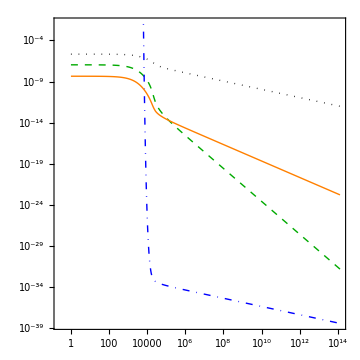

```mathematica
(*plots background quantities: Υ, T, H, and k/a *)
BackgroundPlot
```

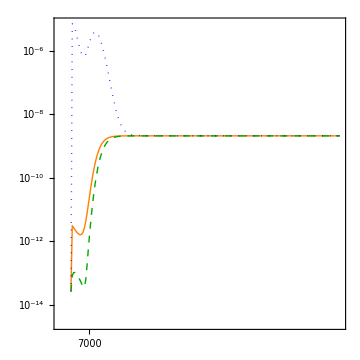

```mathematica
(*plot power spectra*)
PerturbPlot
```

```mathematica
(*plots key background parameters' values at horizon exit, as well as power spectrum and spectral tilt after freeze-out*)
TableForm[table]
```

Log10[λ] | fa [10^12 GeV] | αs | 100 =k/aH, t_init  | ϕ[t_init]/mpl | T/H exit | Υ/3H exit | |ϕdot|/H^2 exit | ϕdot exit | ϕ exit | H exit | A=Rϕ_(k/aH)=10^5 | n_s(pivot*) | r | Rv_(k/aH)=10^5 | n_sv(pivot*) | rv | RT_(k/aH)=10^5 | n_sT(pivot*) | rT
-21 | 0.153 | 0.0269 | 6892.54 | 1.05835 | 7799.76 | 13.9525 | 1.11133×10^8 | -9.79507×10^-13 | 1.01022 | 9.38822×10^-11 | 2.11949×10^-9 | 0.967252 | 2.1179×10^-11 | 2.11949×10^-9 | 0.967252 | 2.1179×10^-11 | 2.11949×10^-9 | 0.967252 | 2.1179×10^-11

```mathematica
(*shows first few lines of background data at each time step*)
TableForm[Take[bckData,4]]
```

t | H | T | k/a | Upsilon | e_r | p_r | e^- | p^- | V | ϕ | dot[ϕ] | dot[T] | dot[H]
1 | 4.4857×10^-9 | 2.158643700660767953850927361458822417716874042526×10^-6 | 6.347382709912319158960422768209694226909441808×10^669 | 1.09032×10^-7 | 7.62553×10^-22 | 2.54184×10^-22 | -2.40075×10^-18 | 2.40176×10^-18 | 2.401×10^-18 | 7. | -0.002497533270995707776335192917827043857 | -3.7226618631195406222516387010220669352×10^-10 | -3.20036×10^-12
1.055667913266337996187555483178860344252349245513127 | 4.48552×10^-9 | 2.158622467210816431739167069322463640150810074763×10^-6 | 6.003641375135492157552480132836409311369964828×10^669 | 1.09028×10^-7 | 7.62523×10^-22 | 2.54174×10^-22 | -2.40056×10^-18 | 2.40157×10^-18 | 2.40080925589700080428958819511731069036334685804×10^-18 | 6.999860969543886690180704084448717282769635475205 | -0.002497461143060048962032943117924258785333669 | -3.903149151176855658846145618195624075540835×10^-10 | -3.20023×10^-12
1.114434743100104522246773235211470529763193953290472 | 4.48533×10^-9 | 2.158599060510878999817655966827956629289866547638×10^-6 | 5.66095618242525628153941098355984541129026719×10^669 | 1.09025×10^-7 | 7.6249×10^-22 | 2.54163×10^-22 | -2.40035×10^-18 | 2.40137×10^-18 | 2.400607911721548076437787347375588885487177158103×10^-18 | 6.999714203869132461539372139664406820770307925118 | -0.0024973867135439837439091893200683904713635269 | -4.0541117054482938687394577269488893335096787×10^-10 | -3.20008×10^-12

```mathematica
(*shows first few lines of power spectrum data at each time step*)
TableForm[Take[powerData,4]]
```

t | PRϕ | PRv | PRT
6892.5371119079927666462026536464691162109375 | 2.6528×10^-14 | 2.6528×10^-14 | 2.6528×10^-14
6900.3342066637280145758258885491098766351569793187 | 3.12903×10^-12 | 8.33255×10^-14 | 7.08763×10^-6
6908.1401314560678007564340462332008740986566408537 | 2.68247×10^-12 | 1.0395×10^-13 | 6.87056×10^-6

### export results

```mathematica
(*exports background plot*)
Export[ToFileName[directoryPath,fileNameBckPlot],BackgroundPlot];
```

```mathematica
(*exports power spectrum plot*)
Export[ToFileName[directoryPath,fileNamePowerSpectrumPlot],PerturbPlot];
```

```mathematica
(*exports key background & freeze-out data*)
Export[ToFileName[directoryPath,fileNameTable],table];
```

```mathematica
(*exports full background data*)
Export[ToFileName[directoryPath,fileNameBck],bckData];
```

```mathematica
(*exports full power spectrum data*)
Export[ToFileName[directoryPath,fileNamePowerSpectrum],powerData];
```